## Probability of single and double resistance for the CLG model with constant or time-dependent birth and death rates

### Input

```mathematica
<<MaTeX`
```

```mathematica
ClearAll["Global`*"]
```

#### Constant rates

```mathematica
dS[t_]:=0.1;
dA[t_]:=0.1;
dB[t_]:=0.1;
dD[t_]:=0.1;
ρS[t_]:=0.9;
ρA[t_]:=1.0;
ρB[t_]:=1.1;
ρD[t_]:=1.2;
μA= 1.0 10^-3;
μB= 1.0 10^-4;
n0 = 1 10^3;
kS=1.1 10^3;
kA= 1.1 10^3;
kB= 1.2 10^3;
kD= 1.3 10^3;
tmax=150;
```

#### Sinusoidal rates

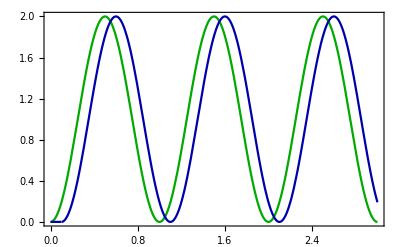

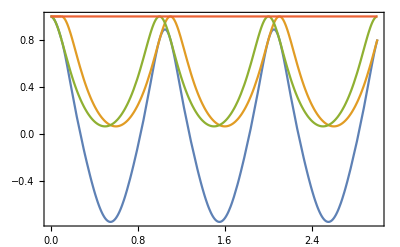

```mathematica
P=1;ΔtA = 0.0; ΔtB=0.1; I0=1.0;
CA[t_]:=Piecewise[{{0,t≤ΔtA},{ I0(Cos[(2Pi (t+P/2-ΔtA))/P]+1),t>ΔtA}}]; 
CB[t_]:=Piecewise[{{0,t≤ΔtB},{I0(Cos[(2Pi (t+P/2-ΔtB))/P]+1),t>ΔtB}}];
μA= 1 10^-3;
μB= 1 10^-3;
fA[t_]:=1+CA[t];fB[t_]:=1+CB[t];
dS[t_]:=0.1fA[t]fB[t];
dA[t_]:=0.1fB[t]; 
dB[t_]:=0.1fA[t];
dD[t_]:=0.1; 
ρS[t_]:=1.1/(fA[t]fB[t])-dS[t]; 
ρA[t_]:=1.1/fB[t]-dA[t];
ρB[t_]:=1.1/fA[t]-dB[t];
ρD[t_]:=1.0;
n0 = 10^4;
tmax=100;
kS=1.0 10^6;
kA= 1.1 10^6;
kB= 1.2 10^6;
kD= 1.3 10^6;
Plot[{CA[t],CB[t]},{t,0,3}, PlotStyle->{Darker[Green],Darker[Blue]},BaseStyle->{FontFamily -> "Latin Modern Roman",FontSize->15},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\text{time(a.u.)}", Magnification->1.5],MaTeX["C \\text{(a.u.)}",Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["C_A", Magnification->1.2],MaTeX["C_B", Magnification->1.2]},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),Spacings->0.15],{0.89,0.82}]]

Plot[{ρS[t],ρA[t],ρB[t],ρD[t]},{t,0,3}, PlotRange->All,BaseStyle->{FontFamily -> "Latin Modern Roman",FontSize->15},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\text{time(a.u.)}", Magnification->1.5],MaTeX["\\text{growth rates}", Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["r_S", Magnification->1.2],MaTeX["r_A", Magnification->1.2],MaTeX["r_B", Magnification->1.2],MaTeX["r_D", Magnification->1.2]},Spacings->0.15,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.89,0.69}]]
```

#### Pulsing rates

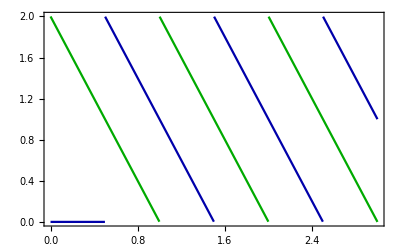

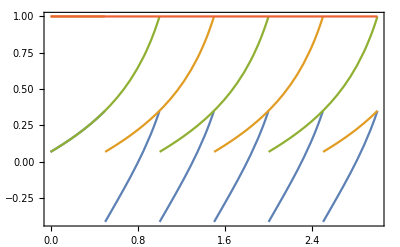

```mathematica
P=1;I0 = 0; I1 = 2.0;ΔtA=0.0; ΔtB =0.5;
CA0[t_]:=(I1-I0)/P^2(-t+ΔtA+P)^1+I0; CA[t_]:=Piecewise[{{0,t≤ΔtA},{ CA0[Mod[t-ΔtA,P]+ΔtA],t>ΔtA}}]; 
CB0[t_]:=(I1-I0)/P^2(-t+ΔtB+P)^1+I0; CB[t_]:=Piecewise[{{0,t≤ΔtB},{ CB0[Mod[t-ΔtB,P]+ΔtB],t>ΔtB}}]; 
fA[t_]:=1+CA[t];fB[t_]:=1+CB[t];
dS[t_]:=0.1fA[t]fB[t];
dA[t_]:=0.1fB[t]; 
dB[t_]:=0.1fA[t];
dD[t_]:=0.1; 
ρS[t_]:=1.1/(fA[t]fB[t])-dS[t]; 
ρA[t_]:=1.1/fB[t]-dA[t];
ρB[t_]:=1.1/fA[t]-dB[t];
ρD[t_]:=1.0;
μA= 1 10^-3;
μB= 1 10^-3;
n0 = 5 10^3;
tmax=100;
kS=1.0 10^4;
kA= 1.1 10^4;
kB= 1.2 10^4;
kD= 1.3 10^4;
Plot[{CA[t],CB[t]},{t,0,3}, PlotStyle->{Darker[Green],Darker[Blue]},BaseStyle->{FontFamily -> "Latin Modern Roman",FontSize->15},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\text{time(a.u.)}", Magnification->1.5],MaTeX["C \\text{(a.u.)}",Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["C_A", Magnification->1.2],MaTeX["C_B", Magnification->1.2]},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.88,0.79}]]
Plot[{ρS[t],ρA[t],ρB[t],ρD[t]},{t,0,3}, BaseStyle->{FontFamily -> "Latin Modern Roman",FontSize->15},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\text{time(a.u.)}", Magnification->1.5],MaTeX["\\text{growth rates}", Magnification->1.5]},PlotLegends->Placed[LineLegend[{MaTeX["r_S", Magnification->1.2],MaTeX["r_A", Magnification->1.2],MaTeX["r_B", Magnification->1.2],MaTeX["r_D", Magnification->1.2]},LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.89,0.61}]]
```

### Mean values

```mathematica
nsol=NDSolve[{nSe'[t]==ρS[t](1-μA-μB)nSe[t](1-nTe[t]/kS)HeavisideTheta[kS-nTe[t]],nAe'[t]==(dS[t]+ρS[t](1-nTe[t]/kS)HeavisideTheta[kS-nTe[t]])μA nSe[t]+ρA[t](1-μB)(1-nTe[t]/kA)HeavisideTheta[kA-nTe[t]]nAe[t],nBe'[t]==(dS[t]+ρS[t](1-nTe[t]/kS)HeavisideTheta[kS-nTe[t]])μB nSe[t]+ρB[t](1-μA)(1-nTe[t]/kB)HeavisideTheta[kB-nTe[t]]nBe[t],nDe'[t]==(dA[t]+ρA[t](1-nTe[t]/kA)HeavisideTheta[kA-nTe[t]])μB nAe[t]+(dB[t]+ρB[t](1-nTe[t]/kB)HeavisideTheta[kB-nTe[t]])μA nBe[t]+ρD[t] (1-nTe[t]/kD)HeavisideTheta[kD-nTe[t]]nDe[t],nSe[0]==n0,nAe[0]==0,nBe[0]==0,nDe[0]==0,nTe[t]==nSe[t] + nAe[t] + nBe[t] + nDe[t]} ,{nSe,nAe,nBe,nDe},{t,0,tmax},Method->{"EventLocator","Event":>{nTe[t]-kS,nTe[t]-kA,nTe[t]-kB,nTe[t]-kD},"EventAction":>{tS=t,tA=t;,tB=t;,tD=t;},"DiscontinuityProcessing"->False}];
{nS, nA,nB,nD}=nsol[[1,All,2]];
nT[t_]:=nS[t] + nA[t] + nB[t] + nD[t];
Print["tS=",tS, ", tA=",tA, ", tB=",tB,  ", tD=",tD]
```

tS=7.36326, tA=7.36326, tB=75.9077, tD=115.894

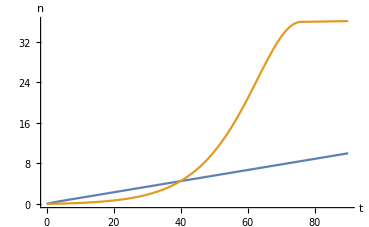

```mathematica
Plot[{nA[t],nB[t]},{t,0,90},PlotRange->All,AxesLabel->{"t","n"}]
```

### P_ext

```mathematica
nsolext=NDSolve[{nAext'[t]==ρA[t](1-μB) nAext[t](1-nT[t]/kA)HeavisideTheta[kA-nT[t]],nBext'[t]==ρB[t](1-μA) nBext[t](1-nT[t]/kB)HeavisideTheta[kB-nT[t]],nDext'[t]==ρD[t]  nDext[t](1-nT[t]/kD)HeavisideTheta[kD-nT[t]],nAext[0]==1,nBext[0]==1,nDext[0]==1} ,{nAext,nBext,nDext},{t,0,tmax}];
{nA0,nB0, nD0}=nsolext[[1,All,2]];
```

```mathematica
nAp[t_ ?NumericQ,tp_ ?NumericQ]:=nA0[tp]/nA0[t];nBp[t_ ?NumericQ,tp_ ?NumericQ]:=nB0[tp]/nB0[t];
nDp[t_ ?NumericQ,tp_ ?NumericQ]:=nD0[tp]/nD0[t];
```

```mathematica
PeFA[t_?NumericQ,T_?NumericQ] := NIntegrate[(dA[tp] (1-μB))/nAp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
PeFB[t_?NumericQ,T_?NumericQ] := NIntegrate[(dB[tp] (1-μA))/nBp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
PeFD[t_?NumericQ,T_?NumericQ] := NIntegrate[dD[tp]/nDp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
```

```mathematica
PextA[t_,T_]:=PeFA[t,T]/(1 + PeFA[t,T]);PextB[t_,T_]:=PeFB[t,T]/(1 + PeFB[t,T]);PextD[t_,T_]:=PeFD[t,T]/(1 + PeFD[t,T]);
```

### Single resistance

```mathematica
Clear[PRSingle]
```

```mathematica
WA[t_]:=nS[t](dS[t]+ρS[t](1-nT[t]/kS)*HeavisideTheta[kS-nT[t]])μA;
WB[t_]:=nS[t](dS[t]+ρS[t](1-nT[t]/kS)*HeavisideTheta[kS-nT[t]])μB;
PRSingle[T_]:=PRSingle[T]=1-Exp[NIntegrate[WA[t](PextA[t,T] - 1) + WB[t](PextB[t,T] - 1),{t,0,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];
```

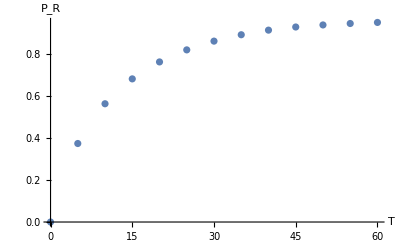

```mathematica
ListPlot[Table[{T,PRSingle[T]},{T,0,60,5}],AxesLabel->{"T","P_R"}]
```

### Double resistance

```mathematica
Clear[PRDouble]
```

```mathematica
WD[t_]:=(dA[t] + ρA[t](1-nT[t]/kA)*HeavisideTheta[kA-nT[t]])μB nA[t] + (dB[t] + ρB[t](1-nT[t]/kB)*HeavisideTheta[kB-nT[t]])μA nB[t];
PhiD[T_]:=NIntegrate[WD[t](PextD[t,T]-1),{t,0,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
PRDouble[T_]:=PRDouble[T]=1-Exp[PhiD[T]];
```

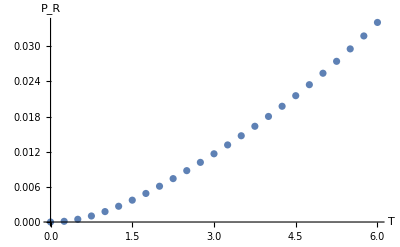

```mathematica
ListPlot[Table[{T,Quiet[PRDouble[T]]},{T,0,6,0.25}],AxesLabel->{"T","P_R"}]
```